# Mathematica Project: Exploratory Data Analysis on ‘Data Scientists’

## A big picture view of the state of data scientists and machine learning engineers.

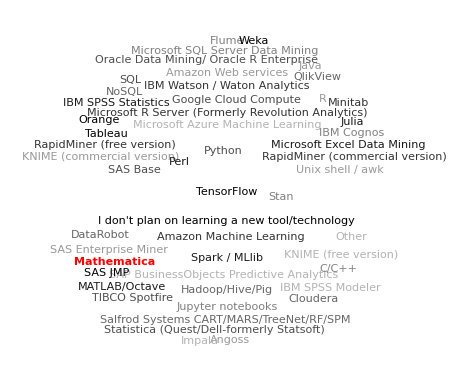

### In this Mathematica project, we will explore the capabilities of Mathematica to better understand the state of data science enthusiasts. The dataset consisting of more than 10,000 rows is obtained from Kaggle, which is a result of ‘Kaggle Survey 2017’. We will explore various capabilities of Mathematica in Data Analysis and Data Visualizations. Further, we will utilize Machine Learning techniques to train models and Classify features with several algorithms, such as Nearest Neighbors, Random Forest.

Dataset : https : // www.kaggle.com/kaggle/kaggle - survey - 2017

## Introduction

Data science is a “concept to unify statistics, data analysis, machine learning and their related methods” in order to “understand and analyze actual phenomena” with data. It employs techniques and theories drawn from many fields within the context of mathematics, statistics, information science, and computer science.
Since we are learning Data Science and Mathematica, it makes sense that we dig deeper in the current trends and the state of Data Scientists around the world. The dataset consisting of more than 16,000 rows is obtained from Kaggle, which is a result of ‘Kaggle Survey 2017’. With this dataset, we will explore the capabilities of Mathematica to gain insights n the data. Firstly, we will dive into Data Analysis and Data Visualization. Further, we will utilize Machine Learning techniques to train models and Classify features with several algorithms, such as Logistic Regression and Neural Network.

Let us import our Dataset using Dataset function and see what our data is.

```mathematica
DatasetCSV= Import["/ABHI/Workspace/Study/UCD/SEM 1/MATHEMATICA FOR RESEARCH/Project/EDA-Data-Scientists/Dataset/multipleChoiceResponses.csv"];
header=DatasetCSV[[1]];
data=DatasetCSV[[2;;]];
DataSet=Thread[header->#]&/@data//Map[Association]//Dataset
```

Dataset[<>]

#### Parameters

We have 16000+ rows and 200+ columns. Of all the columns, we are particularly interested in the following:

Gender: Gender of the individuals.

Country: Native country of the person.

Age: Individual’s Age in years.

Employment Status: Indicating their occupation.

Language: The most used programming language for Data Science.

JobTitle: Their Job Title.

Education: Their most recent degree.

Major: Their Major in College/University.

Tenure: Their experience in Data Science in years.

CompensationAmount: Their annual salary.

CompensationCurrency: Currency of salary.

MLTool: Preferred Machine Learning technology.

CoursePlatform: Preferred Platform for learning.

## Data Analysis

#### Data Duplication Removal

As the first step of Analysis, let us remove the duplicate rows so that we can better analyze the data:

```mathematica
OriginalLength = Length[DataSet];
DataSet = DeleteDuplicates[DataSet];
NewLength = Length[DataSet];
OriginalLength-NewLength
```

321

We removed 321 duplicated rows.

#### Dealing with Empty values

Now that we have removed duplicated data, let us deal with the empty values in the dataset.
While we visualize data, it is inconvenient to have empty values in the data.
So, we have a function to remove the empty values:

```mathematica
RemoveEmptyElements[list_]:=
Module[{returnList= {}},
Quiet[For[i=0,i<Length[list],i++,
If[StringLength[list[[i]]]>0,
AppendTo[returnList,list[[i]]]]]];
returnList];
```

Now that we have our function in place, we will use this while we visualize data.

#### Salary Normalization

Notice that the Salaries (Column CompensationAmount) of Data Scientists are in different currencies (CompensationCurrency). To be able to visualize this and for Machine Learning, it is fair that all the salaries are in the same currencies. So, Let us convert all the salaries to USD so that we can standardize the currency.
The currency conversion rates are in another Dataset file. Let us import it and convert all our currencies to USD:

```mathematica
CurrencyDatasetCSV= Import["/ABHI/Workspace/Study/UCD/SEM 1/MATHEMATICA FOR RESEARCH/Project/EDA-Data-Scientists/Dataset/conversionRates.csv"];
CurrencyHeader=CurrencyDatasetCSV[[1]];
CurrencyData=CurrencyDatasetCSV[[2;;]];
CurrencyDataSet=Thread[CurrencyHeader->#]&/@CurrencyData//Map[Association]//Dataset
```

Dataset[<>]

Let us create a list with Standardized salaries (All salaries in USD):

```mathematica
NormalizedSalaryList = {};
For[i=1,i≤Length[DataSet[All,"CompensationAmount"]],i++,
If[StringLength[DataSet[All,"CompensationCurrency"][[i]]] >0,
Multiplier = CurrencyDataSet[SelectFirst[#originCountry== Normal[DataSet[All,"CompensationCurrency"][[i]]]&],"exchangeRate"];
AppendTo[NormalizedSalaryList,Times[Multiplier, Normal[DataSet[All,"CompensationAmount"][[i]]]]],
AppendTo[NormalizedSalaryList, 0]
];
]
```

We will use this list NormalizedSalaryList in Machine Learning later.

## Data Visualization

Let us have a look at the age of Data Scientists:

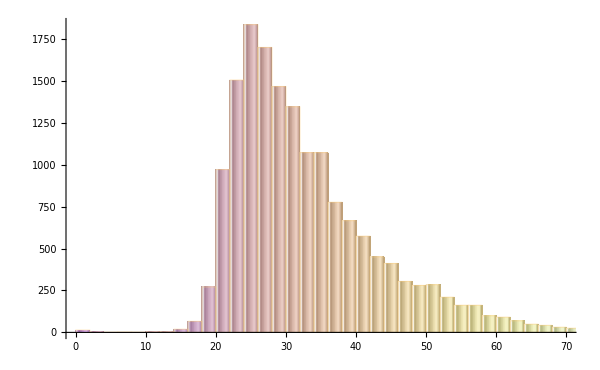

```mathematica
Histogram[DataSet[All,"Age"], 30,
ChartStyle->{"Pastel"},
ChartLabels-> Automatic,
ChartElementFunction->"GlassRectangle",
AxesLabel->Automatic,
ImageSize->{600,400}]
```

We can infer that the median age is between 20 and 35 years.

Gender diversification of Data Scientists:

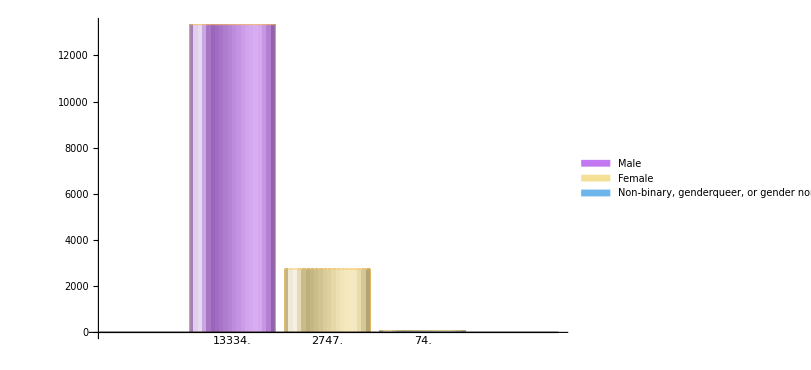

```mathematica
BarChart[Reverse[Sort[Counts[DataSet[All,"GenderSelect"]][[;;3]]]],
ChartElementFunction->"GlassRectangle",
ChartStyle->"Pastel", 
ImageSize->{600,400},
ChartLegends-> Automatic,
LabelingFunction->(Placed[Panel[NumberForm[N@#1]], Below]&)]
```

While most of the Data Scientists are Male, Females are picking up in the recent years.

Coming to the distribution of Data Scientists around the world, here are the top 15 countries with maximum number of Data Science enthusiasts:

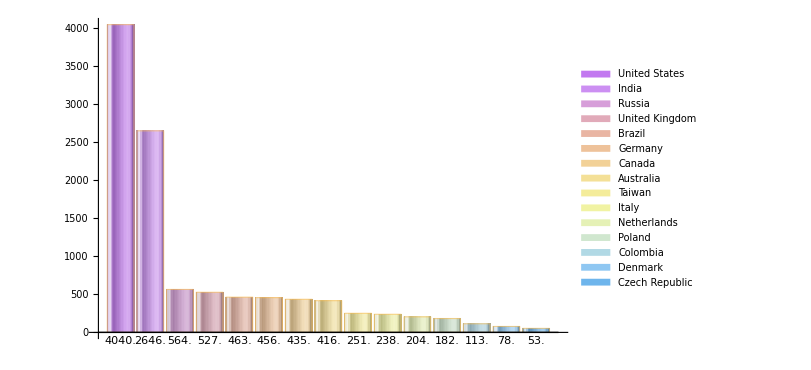

```mathematica
BarChart[Reverse[Sort[Counts[RemoveEmptyElements[DataSet[All,"Country"]]][[;;15]]]],
ChartLegends-> Automatic,
ChartElementFunction->"GlassRectangle",
ChartStyle->"Pastel", 
ImageSize->{600,400},
LabelingFunction->(Placed[Panel[NumberForm[N@#1]], Below]&)]
```

Most of them are concentrated in United States and India.
Also, notice that we have used our function RemoveEmptyElements[] to remove entries that are empty.

Regarding the Job Titles:

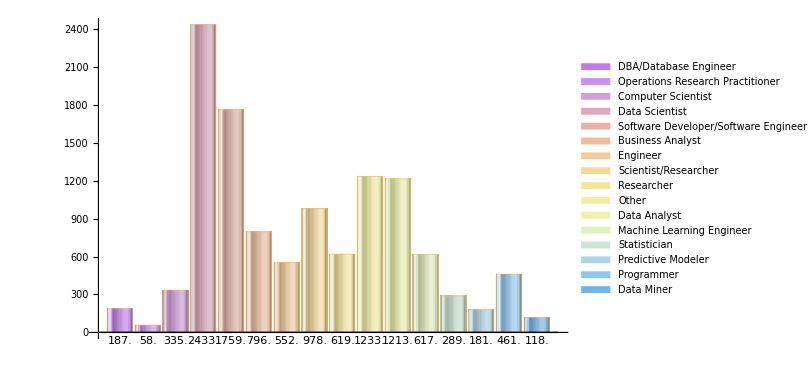

```mathematica
Jobs = RemoveEmptyElements[Normal[DataSet[All,"CurrentJobTitleSelect"]]];
BarChart[Counts[Jobs],
ChartLegends-> Automatic,
ChartElementFunction->"GlassRectangle",
ChartStyle->"Pastel", 
ImageSize->{600,400}, 
LabelingFunction->(Placed[Panel[NumberForm[N@#1]], Below]&)]
```

Most have “Data Scientist” and “Software Developer/Software Engineer” as the Job Position.

The most preferred programming language:

```mathematica
Languages = RemoveEmptyElements[Normal[DataSet[All,"LanguageRecommendationSelect"]]];
PieChart[Reverse[Sort[Counts[Languages]]],
ChartLegends-> Automatic,
ChartStyle->"Pastel", 
ImageSize->{600,400}, 
LabelingFunction->(Placed[Panel[NumberForm[N@#1]], Below]&)]
```

-Graphics-

More than half use Python as their primary language and around 25% use R.

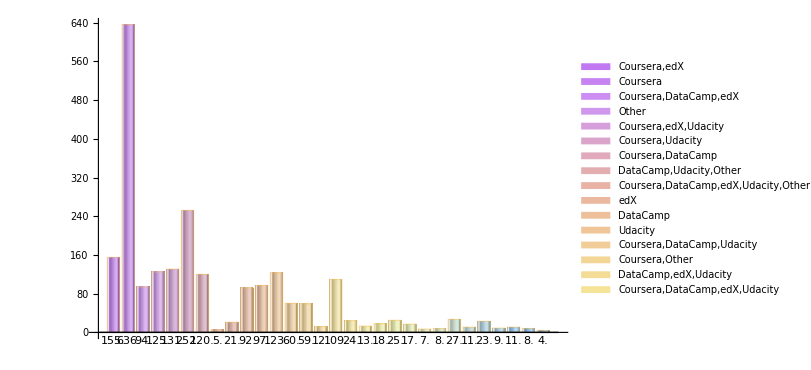

```mathematica
Jobs = RemoveEmptyElements[Normal[DataSet[All,"CoursePlatformSelect"]]];
BarChart[Counts[Jobs],
ChartLegends-> Automatic,
ChartElementFunction->"GlassRectangle",
ChartStyle->"Pastel", 
ImageSize->{600,400}, 
LabelingFunction->(Placed[Panel[NumberForm[N@#1]], Below]&)]
```

Many people prefer “Coursera” to learn Data Science.

Here is a Word Cloud of the most used Machine Learning Technologies:

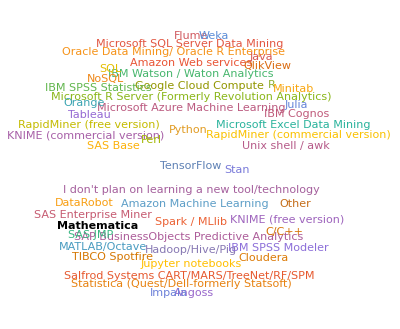

```mathematica
WordCloud[RemoveEmptyElements[Normal[DataSet[All,"MLToolNextYearSelect"]]]]/."Mathematica"->Style["Mathematica",Bold,Black]
```

We notice that even Mathematica is used for Machine Learning (Marked in Black). TensorFlow, Python and R are used a lot.

Let us have a look at the map of countries, with most number of Data Scientists:

```mathematica
CountryList = RemoveEmptyElements[DataSet[All,"Country"]];
CountryList /. "People 's Republic of China" -> "China";
For[i=0,i<Length[CountryList],i++,
Country[CountryList[[i]]] =  Count[CountryList,CountryList[[i]]]
];
CountryValueList = {};
For[i=0,i<Length[CountryList],i++, 
AppendTo[CountryValueList,Interpreter["Country"][CountryList[[i]]] -> Country[CountryList[[i]]]]
];
GeoRegionValuePlot[Union[CountryValueList],
ImageSize->{1200,800},
GeoLabels->(Tooltip[#1,#2]&)]
```

-Graphics-

Let us look at some Statistics of Irish Data Scientists:

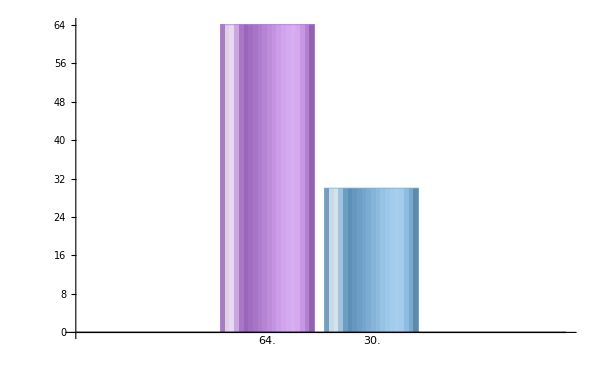

```mathematica
BarChart[Reverse[Sort[Counts[DataSet[Select[#Country== "Ireland"&] ,{"GenderSelect"}]]]],
ChartLegends-> Automatic,
ChartElementFunction->"GlassRectangle",
ChartStyle->"Pastel", 
ImageSize->{600,400},
ChartLegends-> Automatic,
LabelingFunction->(Placed[Panel[NumberForm[N@#1]], Below]&)]
```

Following the global trend, around one third of Irish Data Scientists are women.

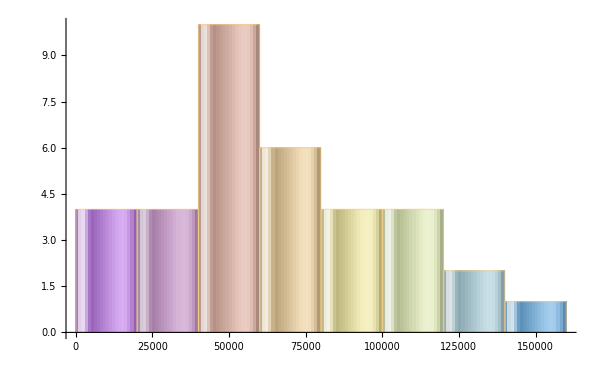

```mathematica
Histogram[DataSet[Select[#Country== "Ireland"&],"CompensationAmount"], 10,
ChartStyle->{"Pastel"},
ChartLabels-> Automatic,
ChartElementFunction->"GlassRectangle",
AxesLabel->Automatic,
ImageSize->{600,400}]
```

Coming to the Salary diversification, many have around EUR 50000 salary with wide variation till EUR 150000.

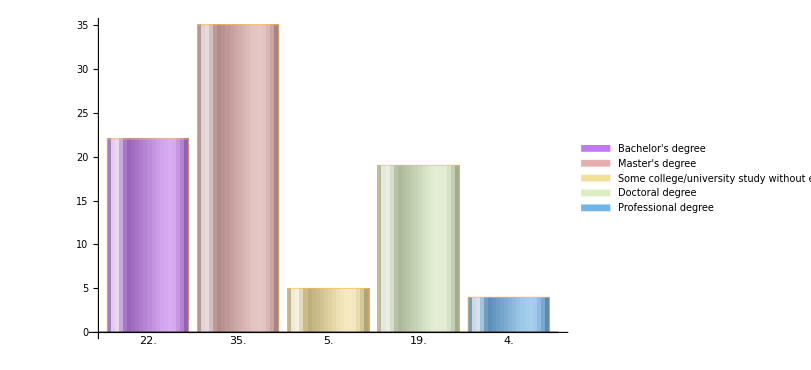

```mathematica
Edu = RemoveEmptyElements[Normal[DataSet[Select[#Country== "Ireland"&],"FormalEducation"]]];
BarChart[Counts[Edu],
ChartLegends-> Automatic,
ChartElementFunction->"GlassRectangle",
ChartStyle->"Pastel", 
ImageSize->{600,400}, 
LabelingFunction->(Placed[Panel[NumberForm[N@#1]], Below]&)]
```

Most Irish Data scientists have a Masters or a Bachelors degree.

## Machine Learning

### Preparation

Let us explore Machine Learning techniques in Mathematica.
We will try and classify the Salary in 3 classes based on all other parameters. Then, we predict the Salary class when the parameters are given.

Firstly, we will construct a dataset with the required columns:

```mathematica
DataSubSet= DataSet[All, {"GenderSelect", "Country", "Age", "CurrentJobTitleSelect", "LanguageRecommendationSelect", "FormalEducation", "MajorSelect", "Tenure", "CompensationAmount", "CompensationCurrency"}]
```

Dataset[<>]

And add a new column with standardized salary: StandardSalary

```mathematica
DataSubSet=MapThread[Append,{Normal[DataSubSet],Thread["StandardSalary"->  NormalizedSalaryList]}]//Dataset
```

Dataset[<>]

We will partition Salary into 3 levels:

```mathematica
SalaryClassify[x_]:=If[StringLength[ToString[x]]>0,Which[x<25000, 1, 25000<x<100000, 2, x>100000, 3, True, 0],0]
```

```mathematica
ClassColumn=Map[SalaryClassify, NormalizedSalaryList]//Normal;
For[i=1,i≤ Length[ClassColumn],i++,
If[Length[Characters[ToString[ClassColumn[[i]]]]]>1,ClassColumn[[i]]=0,];
]
```

For erred values, we assign class 0.

Then, we add this column to our Dataset:

```mathematica
DataSubSet = MapThread[Append,{Normal[DataSubSet],Thread["Class"->  ClassColumn]}]//Dataset;
```

Now, we will split our dataset into Training and Test Datasets with 70:30 ratio.

```mathematica
train = {};
test = {};
For[i=1,i≤ Length[DataSubSet],i++, 
If[RandomInteger[{1,Length[DataSubSet]}]<Length[DataSubSet] 70/100, 
AppendTo[train,Normal[DataSubSet[i,All]]],
AppendTo[test,Normal[DataSubSet[i,All]]]]
]
N[Length[train]/Length[DataSubSet]]
N[Length[test]/Length[DataSubSet]]
trainDataSet= Dataset[train];
testDataSet = Dataset[test];
```

0.698811

0.301189

We prepare the Datasets for ML:

```mathematica
trainsetFeatures = trainDataSet[1;;Length[trainDataSet]-2,{"GenderSelect", "Country", "Age", "CurrentJobTitleSelect", "LanguageRecommendationSelect", "FormalEducation", "MajorSelect", "Tenure", "StandardSalary", "Class"}];
testsetFeatures = testDataSet[1;;Length[testDataSet]-2,{"GenderSelect", "Country", "Age", "CurrentJobTitleSelect", "LanguageRecommendationSelect", "FormalEducation", "MajorSelect", "Tenure", "StandardSalary", "Class"}];
trainsetFinal=Flatten[Normal@trainsetFeatures[1;;Length[trainDataSet]-2,{Most@#->Last@#}&],1];
testsetFinal=Flatten[Normal@testsetFeatures[1;;Length[testDataSet]-2,{Most@#->Last@#}&],1];
```

Notice that we have removed columns “CompensationAmount” and “CompensationCurrency” since we have added Standardized Salary column.

### Classification

Now, we Classify with algorithms:

#### Random Forest:

```mathematica
algoRandomForest=Classify[trainsetFinal,Method->"RandomForest"];
ClassifierInformation[algoRandomForest]
MeasurementsRandomForest=ClassifierMeasurements[algoRandomForest,testsetFinal];
ClassifierMeasurements[algoRandomForest,testsetFinal, "Accuracy"]
```

Classifier information
Input type | Mixed (number: 9)
Classes | ,,0123
Method | RandomForest
Accuracy | 93.4 % ± 0.75 %
Loss | 0.256 ± 0.012
Single evaluation time | 11.3 ms/example
Batch evaluation speed | 2.73 examples/ms
Classifier memory | 858. kB
Training examples used | 11455 examples
Training time | 7.7 s
 |

0.937399

#### Logistic Regression:

```mathematica
algoLogisticRegression=Classify[trainsetFinal,Method->"LogisticRegression"];
ClassifierInformation[algoLogisticRegression]
MeasurementsLogisticRegression=ClassifierMeasurements[algoLogisticRegression,testsetFinal];
ClassifierMeasurements[algoLogisticRegression,testsetFinal, "Accuracy"]
```

Classifier information
Input type | Mixed (number: 9)
Classes | ,,0123
Method | LogisticRegression
Accuracy | 88.9 % ± 0.93 %
Loss | 0.281 ± 0.019
Single evaluation time | 9.29 ms/example
Batch evaluation speed | 3.3 examples/ms
Classifier memory | 716. kB
Training examples used | 11455 examples
Training time | 13.2 s
 |

0.883306

#### Nearest Neighbors:

```mathematica
algoNearestNeighbors=Classify[trainsetFinal,Method->"NearestNeighbors"];
ClassifierInformation[algoNearestNeighbors]
MeasurementsNearestNeighbors=ClassifierMeasurements[algoNearestNeighbors,testsetFinal];
ClassifierMeasurements[algoNearestNeighbors,testsetFinal, "Accuracy"]
```

Classifier information
Input type | Mixed (number: 9)
Classes | ,,0123
Method | NearestNeighbors
Accuracy | 81.8 % ± 0.89 %
Loss | 0.451 ± 0.018
Single evaluation time | 12. ms/example
Batch evaluation speed | 1.65 examples/ms
Classifier memory | 15.6 MB
Training examples used | 11455 examples
Training time | 8.27 s
 |

0.830429

#### Neural Network:

```mathematica
algoNeuralNetwork=Classify[trainsetFinal,Method->"NeuralNetwork"];
ClassifierInformation[algoNeuralNetwork]
MeasurementsNeuralNetwork=ClassifierMeasurements[algoNeuralNetwork,testsetFinal];
ClassifierMeasurements[algoNeuralNetwork,testsetFinal, "Accuracy"]
```

Classifier information
Input type | Mixed (number: 9)
Classes | ,,0123
Method | NeuralNetwork
Accuracy | 84.2 % ± 3.7 %
Loss | 0.577 ± 0.072
Single evaluation time | 15.5 ms/example
Batch evaluation speed | 1.47 examples/ms
Classifier memory | 3.69 MB
Training examples used | 11455 examples
Training time | 1 3
 |

0.807536

### Prediction

We predict the Salary class given other parameters using several Machine Learning Algorithms:

#### Nearest Neighbors:

```mathematica
PredictionNearestNeighbors = Predict[trainsetFinal, Method->"NearestNeighbors"];
PredictionNearestNeighbors[{<|"GenderSelect"->"Female","Country"->"United States","Age"->30,"CurrentJobTitleSelect"->"","LanguageRecommendationSelect"->"Python","FormalEducation"->"Master's degree","MajorSelect"->"Computer Science","Tenure"->"Less than a year","StandardSalary"->15000|>}]
```

{1.}

#### Decision Tree:

```mathematica
PredictionNearestNeighbors = Predict[trainsetFinal, Method->"DecisionTree"];
PredictionNearestNeighbors[{<|"GenderSelect"->"Female","Country"->"United States","Age"->30,"CurrentJobTitleSelect"->"","LanguageRecommendationSelect"->"Python","FormalEducation"->"Master's degree","MajorSelect"->"Computer Science","Tenure"->"Less than a year","StandardSalary"->15000|>}]
```

{1.}

#### Neural Network:

```mathematica
PredictionNearestNeighbors = Predict[trainsetFinal, Method->"NeuralNetwork"];
PredictionNearestNeighbors[{<|"GenderSelect"->"Female","Country"->"United States","Age"->30,"CurrentJobTitleSelect"->"","LanguageRecommendationSelect"->"Python","FormalEducation"->"Master's degree","MajorSelect"->"Computer Science","Tenure"->"Less than a year","StandardSalary"->15000|>}]
```

{1.233}

## Insights

#### Global

We gained the following insights regarding Data Scientists from our analysis and visualization:

Median age is between 20 and 35 years.

Most of the Data Scientists are Male.

Most of them are concentrated in United States and India.

Most have “Data Scientist” and “Software Developer/Software Engineer” as the Job Position.

More than half use Python as their primary language and around 25% use R.

Many people prefer “Coursera” to learn Data Science.

TensorFlow, Python and R are used a lot for Machine Learning.

#### Irish Data Scientists

Around one third of Irish Data Scientists are women.

Many have around EUR 50000 salary .

Most Irish Data scientists have a Masters or a Bachelors degree.

## Conclusion

We gained so many insights from the data regarding Data Scientists and Machine Learning enthusiasts. Regarding the capabilities of Mathematica, it offers excellent features to work with Datasets. Though our Dataset is so large, Mathematica handles the iterations and other intensive tasks withe ease. Even if it takes some processing time, the Machine Learning classifications and predictions run smooth.
In this project, we learned how to work with data, gained insights and explored Mathematica. In conclusion, in addition to its capabilities in Mathematics applications, Mathematica is very well suited for Data Science.